```mathematica
Clear["Global`*"];
```

```mathematica
$Version
```

12.1.0 for Linux x86 (64-bit) (March 14, 2020)

### Required PDF sets:

For this notebook to run, it requires the following PDF sets;

LHA SETS: {CT10,MSTW2008lo68cl,NNPDF30_nlo_as_0118}


PDS SETS:  {ct10.pds,ctq66m.pds}

# Manual file for ManeParse Package Version 5.0

### Version 23.0 18 October 2019 Comments and questions to: Fred Olness olness@physics.smu.edu

## Set Absolute Directory Paths Here

Here we set up all the main directories.
  The rest of the notebook uses only RELATIVE paths.
  We’ll show what goes in each directory below.

```mathematica
(* This just drops the leading path info to make the list of files easier to read *)
(* dropPath=Take[(FileNameSplit /@ # ) //Transpose,-1][[1]]&; *)
dropPath=((Take[#,-1]& /@ (FileNameSplit /@ # )) //Flatten)&
```

Flatten[(Take[#1,-1]&)/@FileNameSplit/@#1]&

```mathematica
(* Remove files that start with "/.*"   
These are the pre-modified CTEQ PDS files and should not be used.  *)
Clear[noDot]
noDot[list_]:=Select[list,!StringMatchQ[#,"*/.*"]&]
```

```mathematica
(* This is where the main notebook file resides *)
workDir=NotebookDirectory[];
FileNames["*",workDir] //dropPath
```

{Demo5.nb,Demo5.pdf,figs4paper_v5.nb,MakeDemo.py,ManeParse_v2.pdf,manual_v5.nb,MP_packages,noe2.perl,PDFDIR,README,README~,User.pdf}

```mathematica
(* This is where the ManeParse files reside *)
dirPackages=workDir<>"/MP_packages";
FileNames["*.m",dirPackages] //dropPath
```

{pdfCalc.m,pdfErrors.m,pdfParseCTEQ.m,pdfParseLHA.m}

```mathematica
(* This is where the LHAPDF files are located *)
lhaDir="/usr/local/share/LHAPDF";
Select[FileNames["*",lhaDir],DirectoryQ]  //dropPath
```

{abm12lhc_5_nnlo,ABMP16_3_nlo,CJ15nlo,CT10,CT10nlo,CT14nlo,CT18ANLO,CT18ANNLO,CT18NLO,CT18NNLO,CT18ptxg,CT18ZNLO,CT18ZNNLO,cteq6,EPPS16nlo_CT14nlo_Ag108,EPPS16nlo_CT14nlo_Al27,EPPS16nlo_CT14nlo_Au197,EPPS16nlo_CT14nlo_Be9,EPPS16nlo_CT14nlo_C12,EPPS16nlo_CT14nlo_Ca40,EPPS16nlo_CT14nlo_Cu64,EPPS16nlo_CT14nlo_Fe56,EPPS16nlo_CT14nlo_He4,EPPS16nlo_CT14nlo_Li6,EPPS16nlo_CT14nlo_Pb208,EPPS16nlo_CT14nlo_Pt195,EPPS16nlo_CT14nlo_Sn119,EPPS16nlo_CT14nlo_W184,HERAPDF20_NLO_VAR,lha_20Rs2,lha_21Rs2,lha_22Rs2,lha_22Rs2ver2,lha_22Rs2ver3,MSTW2008lo68cl,MSTW2008nlo68cl,MSTW2008nnlo68cl,nCTEQ15_108_54,nCTEQ15_1_1,nCTEQ15_119_59,nCTEQ15_12_6,nCTEQ15_131_54,nCTEQ15_14_7,nCTEQ15_184_74,nCTEQ15_197_79,nCTEQ15_197_98,nCTEQ15_20_10,nCTEQ15_207_103,nCTEQ15_208_82,nCTEQ15_2_1,nCTEQ15_27_13,nCTEQ15_3_1,nCTEQ15_3_2,nCTEQ15_40_18,nCTEQ15_40_20,nCTEQ15_4_2,nCTEQ15_56_26,nCTEQ15_56_28,nCTEQ15_6_3,nCTEQ15_64_32,nCTEQ15_7_3,nCTEQ15_84_42,nCTEQ15_9_4,nCTEQ15FullNuc,nCTEQ15FullNuc_108_54,nCTEQ15FullNuc_1_1,nCTEQ15FullNuc_119_59,nCTEQ15FullNuc_12_6,nCTEQ15FullNuc_131_54,nCTEQ15FullNuc_14_7,nCTEQ15FullNuc_184_74,nCTEQ15FullNuc_197_79,nCTEQ15FullNuc_197_98,nCTEQ15FullNuc_20_10,nCTEQ15FullNuc_207_103,nCTEQ15FullNuc_208_82,nCTEQ15FullNuc_2_1,nCTEQ15FullNuc_27_13,nCTEQ15FullNuc_3_2,nCTEQ15FullNuc_40_18,nCTEQ15FullNuc_40_20,nCTEQ15FullNuc_4_2,nCTEQ15FullNuc_56_26,nCTEQ15FullNuc_6_3,nCTEQ15FullNuc_64_32,nCTEQ15FullNuc_7_3,nCTEQ15FullNuc_84_42,nCTEQ15FullNuc_9_4,nCTEQ15np_1_1,nCTEQ15np_208_82,NNPDF30_nlo_as_0118,NNPDF30_nnlo_as_0118,NNPDF30_nnlo_as_0118_nf_6,NNPDF31_nlo_as_0118,NNPDF31_nlo_as_0118_hessian,NNPDF31_nnlo_as_0118,nuanua1_12_6,nuanua1_13_7,nuanua1_16_8,nuanua1_208_82,nuanua1_40_18,nuanua1_56_26,nuanua1FullNuc_12_6,nuanua1FullNuc_13_7,nuanua1FullNuc_16_8,nuanua1FullNuc_208_82,nuanua1FullNuc_40_18,nuanua1FullNuc_56_26}

```mathematica
(* This is where the PDS format files are located *)
pdsDir=workDir<>"/PDFDIR/PDS";
Select[FileNames["*",pdsDir],DirectoryQ]  //dropPath
```

{ct10.pds,ctq66m.pds}

### Required PDF sets:

For this notebook to run, it requires the following PDF sets;

LHA SETS: {CT10,MSTW2008lo68cl,NNPDF30_nlo_as_0118}


PDS SETS:  {ct10.pds,ctq66m.pds}

## Just step through and demo each function:

## Load the packages

#### Loading the main package provides many useful functions

```mathematica
Get[dirPackages<>"/pdfParseLHA.m"]
```

Version: pdfCalc 5.0

Version: ManeParse 5.0: April 2021

- Required Package: pdfCalc --Loaded -

===============================================================

- pdfParseLHA -

Version:  5.0: April 2021

Authors: E.J. Godat, D.B. Clark & F.I. Olness

Please cite: **************

http://ncteq.hepforge.org/code/pdf.html

For a list of available commands, enter: ?pdf*

===============================================================

```mathematica
Get[dirPackages<>"/pdfParseCTEQ.m"]
```

===============================================================

- pdfParseCTEQ -

Version:  5.0:  April 2021

Authors: D.B. Clark, E.J. Godat & F.I. Olness

Please cite: **************

http://ncteq.hepforge.org/code/pdf.html

For a list of available commands, enter: ?pdf*

===============================================================

### pdfCalc.m is already loaded automatically by pdfParseLHA and pdfParseCTEQ, but it won' t hurt to do it again; just ignore the warnings

```mathematica
(* pdfCalc.m is already loaded automatically by pdfParseLHA and pdfParseCTEQ, 
but it won' t hurt to do it again; just ignore the warnings *)

 Get[dirPackages<>"/pdfCalc.m"]
```

Version: pdfCalc 5.0

Version: ManeParse 5.0: April 2021

- Required Package: pdfCalc --Loaded -

SetDelayed::write: Tag pdfReset in pdfReset[] is Protected.

SetDelayed::write: Tag pdfSetListDisplay in pdfSetListDisplay[] is Protected.

SetDelayed::write: Tag pdfSetInterpolator in pdfSetInterpolator[key_:MMA] is Protected.

General::stop: Further output of SetDelayed::write will be suppressed during this calculation.

```mathematica
Get[dirPackages<>"/pdfErrors.m"]
```

===============================================================

- pdfErrors -

Version:  5.0; April 2021

Authors: D.B. Clark, E.J. Godat & F.I. Olness

Please cite: **************

http://ncteq.hepforge.org/code/pdf.html

For a list of available commands, enter: ?pdf*

===============================================================

## Set Interpolator

```mathematica
?pdfSetInterpolator
```

```mathematica
pdfSetInterpolator["MMA"]
```

Default Mathematica interpolator will be used.

```mathematica
pdfSetInterpolator["ManeParse"]
```

ManeParse cubic interpolation will be used.

The x-power of the interpolation is set to 1

```mathematica
?pdfSetXpower
```

```mathematica
pdfSetXpower[]
```

ManeParse cubic interpolation will be used.

The x-power of the interpolation is set to 1

```mathematica
pdfSetXpower[2]
```

ManeParse cubic interpolation will be used.

The x-power of the interpolation is set to 2

```mathematica
pdfSetInterpolator["MMA"]
```

Default Mathematica interpolator will be used.

```mathematica
pdfSetXpower[1.5]
```

ManeParse cubic interpolation will be used.

The x-power of the interpolation is set to 1.5

## pdfReset

```mathematica
pdfReset[]
```

Default Mathematica interpolator will be used.

All internal variables have been reset.

## Read Individual LHAPDF files

### read lhapdf file

```mathematica
lhaList=FileNames["*",lhaDir] //noDot;
(* Remove files that are not directories: i.e., of the form *.*  *)
lhaList=lhaList //Select[#,!StringMatchQ[#,"*.*"]&]& ;
lhaList //dropPath
```

{abm12lhc_5_nnlo,ABMP16_3_nlo,CJ15nlo,CT10,CT10nlo,CT14nlo,CT18ANLO,CT18ANNLO,CT18NLO,CT18NNLO,CT18ptxg,CT18ZNLO,CT18ZNNLO,cteq6,EPPS16nlo_CT14nlo_Ag108,EPPS16nlo_CT14nlo_Al27,EPPS16nlo_CT14nlo_Au197,EPPS16nlo_CT14nlo_Be9,EPPS16nlo_CT14nlo_C12,EPPS16nlo_CT14nlo_Ca40,EPPS16nlo_CT14nlo_Cu64,EPPS16nlo_CT14nlo_Fe56,EPPS16nlo_CT14nlo_He4,EPPS16nlo_CT14nlo_Li6,EPPS16nlo_CT14nlo_Pb208,EPPS16nlo_CT14nlo_Pt195,EPPS16nlo_CT14nlo_Sn119,EPPS16nlo_CT14nlo_W184,HERAPDF20_NLO_VAR,lha_20Rs2,lha_21Rs2,lha_22Rs2,lha_22Rs2ver2,lha_22Rs2ver3,MSTW2008lo68cl,MSTW2008nlo68cl,MSTW2008nnlo68cl,nCTEQ15_108_54,nCTEQ15_1_1,nCTEQ15_119_59,nCTEQ15_12_6,nCTEQ15_131_54,nCTEQ15_14_7,nCTEQ15_184_74,nCTEQ15_197_79,nCTEQ15_197_98,nCTEQ15_20_10,nCTEQ15_207_103,nCTEQ15_208_82,nCTEQ15_2_1,nCTEQ15_27_13,nCTEQ15_3_1,nCTEQ15_3_2,nCTEQ15_40_18,nCTEQ15_40_20,nCTEQ15_4_2,nCTEQ15_56_26,nCTEQ15_56_28,nCTEQ15_6_3,nCTEQ15_64_32,nCTEQ15_7_3,nCTEQ15_84_42,nCTEQ15_9_4,nCTEQ15FullNuc,nCTEQ15FullNuc_108_54,nCTEQ15FullNuc_1_1,nCTEQ15FullNuc_119_59,nCTEQ15FullNuc_12_6,nCTEQ15FullNuc_131_54,nCTEQ15FullNuc_14_7,nCTEQ15FullNuc_184_74,nCTEQ15FullNuc_197_79,nCTEQ15FullNuc_197_98,nCTEQ15FullNuc_20_10,nCTEQ15FullNuc_207_103,nCTEQ15FullNuc_208_82,nCTEQ15FullNuc_2_1,nCTEQ15FullNuc_27_13,nCTEQ15FullNuc_3_2,nCTEQ15FullNuc_40_18,nCTEQ15FullNuc_40_20,nCTEQ15FullNuc_4_2,nCTEQ15FullNuc_56_26,nCTEQ15FullNuc_6_3,nCTEQ15FullNuc_64_32,nCTEQ15FullNuc_7_3,nCTEQ15FullNuc_84_42,nCTEQ15FullNuc_9_4,nCTEQ15np_1_1,nCTEQ15np_208_82,NNPDF30_nlo_as_0118,NNPDF30_nnlo_as_0118,NNPDF30_nnlo_as_0118_nf_6,NNPDF31_nlo_as_0118,NNPDF31_nlo_as_0118_hessian,NNPDF31_nnlo_as_0118,nuanua1_12_6,nuanua1_13_7,nuanua1_16_8,nuanua1_208_82,nuanua1_40_18,nuanua1_56_26,nuanua1FullNuc_12_6,nuanua1FullNuc_13_7,nuanua1FullNuc_16_8,nuanua1FullNuc_208_82,nuanua1FullNuc_40_18,nuanua1FullNuc_56_26}

```mathematica
file=Select[lhaList,StringMatchQ[#,"*CT10nlo"]&]
```

{/usr/local/share/LHAPDF/CT10nlo}

```mathematica
FileNames["*",file //First] //noDot //dropPath
```

{CT10nlo_0000.dat,CT10nlo_0001.dat,CT10nlo_0002.dat,CT10nlo_0003.dat,CT10nlo_0004.dat,CT10nlo_0005.dat,CT10nlo_0006.dat,CT10nlo_0007.dat,CT10nlo_0008.dat,CT10nlo_0009.dat,CT10nlo_0010.dat,CT10nlo_0011.dat,CT10nlo_0012.dat,CT10nlo_0013.dat,CT10nlo_0014.dat,CT10nlo_0015.dat,CT10nlo_0016.dat,CT10nlo_0017.dat,CT10nlo_0018.dat,CT10nlo_0019.dat,CT10nlo_0020.dat,CT10nlo_0021.dat,CT10nlo_0022.dat,CT10nlo_0023.dat,CT10nlo_0024.dat,CT10nlo_0025.dat,CT10nlo_0026.dat,CT10nlo_0027.dat,CT10nlo_0028.dat,CT10nlo_0029.dat,CT10nlo_0030.dat,CT10nlo_0031.dat,CT10nlo_0032.dat,CT10nlo_0033.dat,CT10nlo_0034.dat,CT10nlo_0035.dat,CT10nlo_0036.dat,CT10nlo_0037.dat,CT10nlo_0038.dat,CT10nlo_0039.dat,CT10nlo_0040.dat,CT10nlo_0041.dat,CT10nlo_0042.dat,CT10nlo_0043.dat,CT10nlo_0044.dat,CT10nlo_0045.dat,CT10nlo_0046.dat,CT10nlo_0047.dat,CT10nlo_0048.dat,CT10nlo_0049.dat,CT10nlo_0050.dat,CT10nlo_0051.dat,CT10nlo_0052.dat,CT10nlo.info}

```mathematica
?pdfParseLHA
```

#### Read in First LHA file

```mathematica
file=Select[lhaList,StringMatchQ[#,"*CT10nlo"]&]
files=FileNames["*",file //First]  //noDot;
files //dropPath //Short
```

{/usr/local/share/LHAPDF/CT10nlo}

{CT10nlo_0000.dat,CT10nlo_0001.dat,CT10nlo_0002.dat,CT10nlo_0003.dat,CT10nlo_0004.dat,«45»,CT10nlo_0050.dat,CT10nlo_0051.dat,CT10nlo_0052.dat,CT10nlo.info}

```mathematica
info= Select[files, StringMatchQ[#,"*.info"]&] //First
```

/usr/local/share/LHAPDF/CT10nlo/CT10nlo.info

```mathematica
dat= Select[files,StringMatchQ[#,"*.dat"]&] //First
```

/usr/local/share/LHAPDF/CT10nlo/CT10nlo_0000.dat

```mathematica
pdfParseLHA[info,dat]
```

Successfully read /usr/local/share/LHAPDF/CT10nlo/CT10nlo.info.

Successfully read /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0000.dat.

1

#### Read in Second LHA file

```mathematica
file=Select[lhaList,StringMatchQ[#,"*MSTW2008lo68cl"]&]
files=FileNames["*",file //First]  //noDot;
files //dropPath //Short

info= Select[files,StringMatchQ[#,"*.info"]&] //First
dat= Select[files,StringMatchQ[#,"*.dat"]&] //First
```

{/usr/local/share/LHAPDF/MSTW2008lo68cl}

{MSTW2008lo68cl_0000.dat,MSTW2008lo68cl_0001.dat,MSTW2008lo68cl_0002.dat,«36»,MSTW2008lo68cl_0039.dat,MSTW2008lo68cl_0040.dat,MSTW2008lo68cl.info}

/usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl.info

/usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0000.dat

```mathematica
pdfParseLHA[info,dat]
```

Successfully read /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl.info.

Successfully read /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0000.dat.

2

#### Read in Third LHA file

```mathematica
file=Select[lhaList,StringMatchQ[#,"*NNPDF30_nlo_as_0118"]&]
files=FileNames["*",file //First]  //noDot;
files //dropPath //Short

info= Select[files,StringMatchQ[#,"*.info"]&] //First
dat= Select[files,StringMatchQ[#,"*.dat"]&] //First
```

{/usr/local/share/LHAPDF/NNPDF30_nlo_as_0118}

{NNPDF30_nlo_as_0118_0000.dat,NNPDF30_nlo_as_0118_0001.dat,NNPDF30_nlo_as_0118_0002.dat,«96»,NNPDF30_nlo_as_0118_0099.dat,NNPDF30_nlo_as_0118_0100.dat,NNPDF30_nlo_as_0118.info}

/usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118.info

/usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0000.dat

```mathematica
pdfParseLHA[info,dat]
```

Successfully read /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118.info.

Successfully read /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0000.dat.

3

## Read Individual PDS files

### read PDS files

```mathematica
pdsList=FileNames["*",pdsDir];
pdsList //dropPath
```

{ct10.pds,ctq66m.pds}

```mathematica
?pdfParseCTEQ
```

#### Read in First PDS file

```mathematica
file=Select[pdsList,StringMatchQ[#,"*ct10.pds"]&]
files=FileNames["*",file //First]  //noDot;
files //dropPath //Short
```

{/home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo//PDFDIR/PDS/ct10.pds}

{ct10.00.pds,ct10.01.pds,ct10.02.pds,ct10.03.pds,ct10.04.pds,ct10.05.pds,«41»,ct10.47.pds,ct10.48.pds,ct10.49.pds,ct10.50.pds,ct10.51.pds,ct10.52.pds}

```mathematica
pdfParseCTEQ[files //First]
```

PDF Table for Fit #: cx22a

4

#### Read in Second PDS file

```mathematica
file=Select[pdsList,StringMatchQ[#,"*ctq66m.pds"]&]
files=FileNames["*",file //First]  //noDot;
files //dropPath //Short
```

{/home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo//PDFDIR/PDS/ctq66m.pds}

{ctq66.00.pds,ctq66.01.pds,ctq66.02.pds,ctq66.03.pds,ctq66.04.pds,ctq66.05.pds,«33»,ctq66.39.pds,ctq66.40.pds,ctq66.41.pds,ctq66.42.pds,ctq66.43.pds,ctq66.44.pds}

```mathematica
pdfParseCTEQ[files //First]
```

PDF Table for Fit #: p82a3

5

## Current PDFs

```mathematica
pdfSetListDisplay[]
```

Set Number | File Name | Max Flavors | Valance Flavors
1 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0000.dat | 5 | n/a
2 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0000.dat | 5 | n/a
3 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0000.dat | 5 | n/a
4 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo//PDFDIR/PDS/ct10.pds/ct10.00.pds | 5 | 2
5 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo//PDFDIR/PDS/ctq66m.pds/ctq66.00.pds | 5 | 2

```mathematica
isetMax=Length[pdfSetList]
```

5

```mathematica
Table[{iSet,pdfFunction[iSet,0,0.1,10.]},{iSet,1,isetMax}] //TableForm
```

1 | 11.2014
2 | 10.873
3 | 12.207
4 | 11.2111
5 | 11.0883

## PDF short-hand:

#### We save the short name "pdf" for a user defined function. If you wish, you can put in some error checking or impose boundaries or positivity here.

```mathematica
pdf[args___]:=pdfFunction[args]
SetAttributes[pdf,Listable];
```

```mathematica
Range[isetMax]
```

{1,2,3,4,5}

```mathematica
pdf[Range[isetMax],0,0.1,10.]//TableForm
```

11.2014
10.873
12.207
11.2111
11.0883

```mathematica
pdfPositive[args__]:=Module[{},
tmp=pdf[args];
tmp=Max[tmp,0.0];
Return[tmp];
]

{pdf[1,0,0.9,2.0],pdfPositive[1,0,0.9,2.0]}
```

{0.000336604,0.000336604}

## pdfReset

```mathematica
pdfReset[]
```

Default Mathematica interpolator will be used.

All internal variables have been reset.

## Read Groups of LHAPDF files

### read lhapdf file

```mathematica
lhaList=FileNames["*",lhaDir] //Select[#,!StringMatchQ[#,"*.*"]&]&; 
(* Remove "pdfsets.index" and similar *)
lhaList //dropPath
```

{abm12lhc_5_nnlo,ABMP16_3_nlo,CJ15nlo,CT10,CT10nlo,CT14nlo,CT18ANLO,CT18ANNLO,CT18NLO,CT18NNLO,CT18ptxg,CT18ZNLO,CT18ZNNLO,cteq6,EPPS16nlo_CT14nlo_Ag108,EPPS16nlo_CT14nlo_Al27,EPPS16nlo_CT14nlo_Au197,EPPS16nlo_CT14nlo_Be9,EPPS16nlo_CT14nlo_C12,EPPS16nlo_CT14nlo_Ca40,EPPS16nlo_CT14nlo_Cu64,EPPS16nlo_CT14nlo_Fe56,EPPS16nlo_CT14nlo_He4,EPPS16nlo_CT14nlo_Li6,EPPS16nlo_CT14nlo_Pb208,EPPS16nlo_CT14nlo_Pt195,EPPS16nlo_CT14nlo_Sn119,EPPS16nlo_CT14nlo_W184,HERAPDF20_NLO_VAR,lha_20Rs2,lha_21Rs2,lha_22Rs2,lha_22Rs2ver2,lha_22Rs2ver3,MSTW2008lo68cl,MSTW2008nlo68cl,MSTW2008nnlo68cl,nCTEQ15_108_54,nCTEQ15_1_1,nCTEQ15_119_59,nCTEQ15_12_6,nCTEQ15_131_54,nCTEQ15_14_7,nCTEQ15_184_74,nCTEQ15_197_79,nCTEQ15_197_98,nCTEQ15_20_10,nCTEQ15_207_103,nCTEQ15_208_82,nCTEQ15_2_1,nCTEQ15_27_13,nCTEQ15_3_1,nCTEQ15_3_2,nCTEQ15_40_18,nCTEQ15_40_20,nCTEQ15_4_2,nCTEQ15_56_26,nCTEQ15_56_28,nCTEQ15_6_3,nCTEQ15_64_32,nCTEQ15_7_3,nCTEQ15_84_42,nCTEQ15_9_4,nCTEQ15FullNuc,nCTEQ15FullNuc_108_54,nCTEQ15FullNuc_1_1,nCTEQ15FullNuc_119_59,nCTEQ15FullNuc_12_6,nCTEQ15FullNuc_131_54,nCTEQ15FullNuc_14_7,nCTEQ15FullNuc_184_74,nCTEQ15FullNuc_197_79,nCTEQ15FullNuc_197_98,nCTEQ15FullNuc_20_10,nCTEQ15FullNuc_207_103,nCTEQ15FullNuc_208_82,nCTEQ15FullNuc_2_1,nCTEQ15FullNuc_27_13,nCTEQ15FullNuc_3_2,nCTEQ15FullNuc_40_18,nCTEQ15FullNuc_40_20,nCTEQ15FullNuc_4_2,nCTEQ15FullNuc_56_26,nCTEQ15FullNuc_6_3,nCTEQ15FullNuc_64_32,nCTEQ15FullNuc_7_3,nCTEQ15FullNuc_84_42,nCTEQ15FullNuc_9_4,nCTEQ15np_1_1,nCTEQ15np_208_82,NNPDF30_nlo_as_0118,NNPDF30_nnlo_as_0118,NNPDF30_nnlo_as_0118_nf_6,NNPDF31_nlo_as_0118,NNPDF31_nlo_as_0118_hessian,NNPDF31_nnlo_as_0118,nuanua1_12_6,nuanua1_13_7,nuanua1_16_8,nuanua1_208_82,nuanua1_40_18,nuanua1_56_26,nuanua1FullNuc_12_6,nuanua1FullNuc_13_7,nuanua1FullNuc_16_8,nuanua1FullNuc_208_82,nuanua1FullNuc_40_18,nuanua1FullNuc_56_26}

```mathematica
?pdfFamilyParseLHA
```

#### Read in First LHA file group

```mathematica
file=Select[lhaList,StringMatchQ[#,"*CT10nlo"]&]
```

{/usr/local/share/LHAPDF/CT10nlo}

```mathematica
ct10=pdfFamilyParseLHA[file //First]
```

Successfully read /usr/local/share/LHAPDF/CT10nlo/CT10nlo.info.

Included 53 files in the PDF family.

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53}

#### Read in Second LHA file group

```mathematica
file=Select[lhaList,StringMatchQ[#,"*MSTW2008lo68cl"]&]
```

{/usr/local/share/LHAPDF/MSTW2008lo68cl}

```mathematica
mstw=pdfFamilyParseLHA[file //First]
```

Successfully read /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl.info.

Included 41 files in the PDF family.

{54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94}

#### Read in Third LHA file group

```mathematica
file=Select[lhaList,StringMatchQ[#,"*NNPDF30_nlo_as_0118"]&]
```

{/usr/local/share/LHAPDF/NNPDF30_nlo_as_0118}

```mathematica
nnpdf=pdfFamilyParseLHA[file //First]
```

Successfully read /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118.info.

Included 101 files in the PDF family.

{95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195}

## Read Groups of PDS files

### read pds file

```mathematica
pdsList=FileNames["*",pdsDir];
pdsList //dropPath
```

{ct10.pds,ctq66m.pds}

```mathematica
?pdfFamilyParseCTEQ
```

#### Read in First PDS file group

```mathematica
file=Select[pdsList,StringMatchQ[#,"*ct10.pds"]&]
```

{/home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo//PDFDIR/PDS/ct10.pds}

```mathematica
ct10pds=pdfFamilyParseCTEQ[file //First]
```

General::munfl: 5.91609/(1.×10^315) is too small to represent as a normalized machine number; precision may be lost.

/home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.35.pds was not initialized: 2 error messages

Included 52 files in the PDF family.

{196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247}

#### Read in Second PDS file group

```mathematica
file=Select[pdsList,StringMatchQ[#,"*ctq66m.pds"]&]
```

{/home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo//PDFDIR/PDS/ctq66m.pds}

```mathematica
cteq66=pdfFamilyParseCTEQ[file //First]
```

Included 45 files in the PDF family.

{248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292}

## Current PDFs

```mathematica
pdfSetListDisplay[]
```

Set Number | File Name | Max Flavors | Valance Flavors
1 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0000.dat | 5 | n/a
2 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0001.dat | 5 | n/a
3 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0002.dat | 5 | n/a
4 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0003.dat | 5 | n/a
5 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0004.dat | 5 | n/a
6 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0005.dat | 5 | n/a
7 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0006.dat | 5 | n/a
8 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0007.dat | 5 | n/a
9 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0008.dat | 5 | n/a
10 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0009.dat | 5 | n/a
11 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0010.dat | 5 | n/a
12 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0011.dat | 5 | n/a
13 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0012.dat | 5 | n/a
14 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0013.dat | 5 | n/a
15 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0014.dat | 5 | n/a
16 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0015.dat | 5 | n/a
17 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0016.dat | 5 | n/a
18 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0017.dat | 5 | n/a
19 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0018.dat | 5 | n/a
20 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0019.dat | 5 | n/a
21 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0020.dat | 5 | n/a
22 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0021.dat | 5 | n/a
23 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0022.dat | 5 | n/a
24 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0023.dat | 5 | n/a
25 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0024.dat | 5 | n/a
26 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0025.dat | 5 | n/a
27 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0026.dat | 5 | n/a
28 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0027.dat | 5 | n/a
29 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0028.dat | 5 | n/a
30 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0029.dat | 5 | n/a
31 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0030.dat | 5 | n/a
32 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0031.dat | 5 | n/a
33 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0032.dat | 5 | n/a
34 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0033.dat | 5 | n/a
35 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0034.dat | 5 | n/a
36 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0035.dat | 5 | n/a
37 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0036.dat | 5 | n/a
38 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0037.dat | 5 | n/a
39 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0038.dat | 5 | n/a
40 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0039.dat | 5 | n/a
41 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0040.dat | 5 | n/a
42 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0041.dat | 5 | n/a
43 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0042.dat | 5 | n/a
44 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0043.dat | 5 | n/a
45 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0044.dat | 5 | n/a
46 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0045.dat | 5 | n/a
47 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0046.dat | 5 | n/a
48 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0047.dat | 5 | n/a
49 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0048.dat | 5 | n/a
50 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0049.dat | 5 | n/a
51 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0050.dat | 5 | n/a
52 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0051.dat | 5 | n/a
53 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0052.dat | 5 | n/a
54 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0000.dat | 5 | n/a
55 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0001.dat | 5 | n/a
56 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0002.dat | 5 | n/a
57 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0003.dat | 5 | n/a
58 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0004.dat | 5 | n/a
59 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0005.dat | 5 | n/a
60 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0006.dat | 5 | n/a
61 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0007.dat | 5 | n/a
62 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0008.dat | 5 | n/a
63 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0009.dat | 5 | n/a
64 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0010.dat | 5 | n/a
65 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0011.dat | 5 | n/a
66 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0012.dat | 5 | n/a
67 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0013.dat | 5 | n/a
68 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0014.dat | 5 | n/a
69 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0015.dat | 5 | n/a
70 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0016.dat | 5 | n/a
71 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0017.dat | 5 | n/a
72 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0018.dat | 5 | n/a
73 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0019.dat | 5 | n/a
74 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0020.dat | 5 | n/a
75 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0021.dat | 5 | n/a
76 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0022.dat | 5 | n/a
77 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0023.dat | 5 | n/a
78 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0024.dat | 5 | n/a
79 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0025.dat | 5 | n/a
80 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0026.dat | 5 | n/a
81 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0027.dat | 5 | n/a
82 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0028.dat | 5 | n/a
83 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0029.dat | 5 | n/a
84 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0030.dat | 5 | n/a
85 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0031.dat | 5 | n/a
86 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0032.dat | 5 | n/a
87 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0033.dat | 5 | n/a
88 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0034.dat | 5 | n/a
89 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0035.dat | 5 | n/a
90 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0036.dat | 5 | n/a
91 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0037.dat | 5 | n/a
92 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0038.dat | 5 | n/a
93 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0039.dat | 5 | n/a
94 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0040.dat | 5 | n/a
95 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0000.dat | 5 | n/a
96 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0001.dat | 5 | n/a
97 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0002.dat | 5 | n/a
98 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0003.dat | 5 | n/a
99 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0004.dat | 5 | n/a
100 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0005.dat | 5 | n/a
101 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0006.dat | 5 | n/a
102 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0007.dat | 5 | n/a
103 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0008.dat | 5 | n/a
104 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0009.dat | 5 | n/a
105 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0010.dat | 5 | n/a
106 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0011.dat | 5 | n/a
107 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0012.dat | 5 | n/a
108 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0013.dat | 5 | n/a
109 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0014.dat | 5 | n/a
110 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0015.dat | 5 | n/a
111 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0016.dat | 5 | n/a
112 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0017.dat | 5 | n/a
113 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0018.dat | 5 | n/a
114 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0019.dat | 5 | n/a
115 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0020.dat | 5 | n/a
116 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0021.dat | 5 | n/a
117 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0022.dat | 5 | n/a
118 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0023.dat | 5 | n/a
119 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0024.dat | 5 | n/a
120 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0025.dat | 5 | n/a
121 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0026.dat | 5 | n/a
122 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0027.dat | 5 | n/a
123 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0028.dat | 5 | n/a
124 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0029.dat | 5 | n/a
125 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0030.dat | 5 | n/a
126 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0031.dat | 5 | n/a
127 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0032.dat | 5 | n/a
128 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0033.dat | 5 | n/a
129 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0034.dat | 5 | n/a
130 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0035.dat | 5 | n/a
131 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0036.dat | 5 | n/a
132 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0037.dat | 5 | n/a
133 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0038.dat | 5 | n/a
134 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0039.dat | 5 | n/a
135 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0040.dat | 5 | n/a
136 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0041.dat | 5 | n/a
137 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0042.dat | 5 | n/a
138 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0043.dat | 5 | n/a
139 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0044.dat | 5 | n/a
140 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0045.dat | 5 | n/a
141 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0046.dat | 5 | n/a
142 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0047.dat | 5 | n/a
143 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0048.dat | 5 | n/a
144 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0049.dat | 5 | n/a
145 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0050.dat | 5 | n/a
146 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0051.dat | 5 | n/a
147 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0052.dat | 5 | n/a
148 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0053.dat | 5 | n/a
149 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0054.dat | 5 | n/a
150 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0055.dat | 5 | n/a
151 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0056.dat | 5 | n/a
152 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0057.dat | 5 | n/a
153 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0058.dat | 5 | n/a
154 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0059.dat | 5 | n/a
155 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0060.dat | 5 | n/a
156 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0061.dat | 5 | n/a
157 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0062.dat | 5 | n/a
158 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0063.dat | 5 | n/a
159 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0064.dat | 5 | n/a
160 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0065.dat | 5 | n/a
161 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0066.dat | 5 | n/a
162 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0067.dat | 5 | n/a
163 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0068.dat | 5 | n/a
164 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0069.dat | 5 | n/a
165 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0070.dat | 5 | n/a
166 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0071.dat | 5 | n/a
167 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0072.dat | 5 | n/a
168 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0073.dat | 5 | n/a
169 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0074.dat | 5 | n/a
170 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0075.dat | 5 | n/a
171 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0076.dat | 5 | n/a
172 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0077.dat | 5 | n/a
173 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0078.dat | 5 | n/a
174 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0079.dat | 5 | n/a
175 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0080.dat | 5 | n/a
176 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0081.dat | 5 | n/a
177 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0082.dat | 5 | n/a
178 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0083.dat | 5 | n/a
179 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0084.dat | 5 | n/a
180 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0085.dat | 5 | n/a
181 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0086.dat | 5 | n/a
182 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0087.dat | 5 | n/a
183 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0088.dat | 5 | n/a
184 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0089.dat | 5 | n/a
185 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0090.dat | 5 | n/a
186 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0091.dat | 5 | n/a
187 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0092.dat | 5 | n/a
188 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0093.dat | 5 | n/a
189 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0094.dat | 5 | n/a
190 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0095.dat | 5 | n/a
191 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0096.dat | 5 | n/a
192 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0097.dat | 5 | n/a
193 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0098.dat | 5 | n/a
194 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0099.dat | 5 | n/a
195 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0100.dat | 5 | n/a
196 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.00.pds | 5 | 2
197 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.01.pds | 5 | 2
198 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.02.pds | 5 | 2
199 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.03.pds | 5 | 2
200 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.04.pds | 5 | 2
201 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.05.pds | 5 | 2
202 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.06.pds | 5 | 2
203 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.07.pds | 5 | 2
204 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.08.pds | 5 | 2
205 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.09.pds | 5 | 2
206 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.10.pds | 5 | 2
207 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.11.pds | 5 | 2
208 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.12.pds | 5 | 2
209 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.13.pds | 5 | 2
210 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.14.pds | 5 | 2
211 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.15.pds | 5 | 2
212 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.16.pds | 5 | 2
213 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.17.pds | 5 | 2
214 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.18.pds | 5 | 2
215 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.19.pds | 5 | 2
216 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.20.pds | 5 | 2
217 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.21.pds | 5 | 2
218 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.22.pds | 5 | 2
219 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.23.pds | 5 | 2
220 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.24.pds | 5 | 2
221 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.25.pds | 5 | 2
222 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.26.pds | 5 | 2
223 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.27.pds | 5 | 2
224 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.28.pds | 5 | 2
225 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.29.pds | 5 | 2
226 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.30.pds | 5 | 2
227 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.31.pds | 5 | 2
228 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.32.pds | 5 | 2
229 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.33.pds | 5 | 2
230 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.34.pds | 5 | 2
231 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.36.pds | 5 | 2
232 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.37.pds | 5 | 2
233 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.38.pds | 5 | 2
234 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.39.pds | 5 | 2
235 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.40.pds | 5 | 2
236 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.41.pds | 5 | 2
237 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.42.pds | 5 | 2
238 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.43.pds | 5 | 2
239 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.44.pds | 5 | 2
240 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.45.pds | 5 | 2
241 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.46.pds | 5 | 2
242 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.47.pds | 5 | 2
243 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.48.pds | 5 | 2
244 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.49.pds | 5 | 2
245 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.50.pds | 5 | 2
246 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.51.pds | 5 | 2
247 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.52.pds | 5 | 2
248 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.00.pds | 5 | 2
249 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.01.pds | 5 | 2
250 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.02.pds | 5 | 2
251 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.03.pds | 5 | 2
252 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.04.pds | 5 | 2
253 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.05.pds | 5 | 2
254 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.06.pds | 5 | 2
255 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.07.pds | 5 | 2
256 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.08.pds | 5 | 2
257 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.09.pds | 5 | 2
258 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.10.pds | 5 | 2
259 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.11.pds | 5 | 2
260 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.12.pds | 5 | 2
261 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.13.pds | 5 | 2
262 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.14.pds | 5 | 2
263 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.15.pds | 5 | 2
264 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.16.pds | 5 | 2
265 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.17.pds | 5 | 2
266 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.18.pds | 5 | 2
267 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.19.pds | 5 | 2
268 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.20.pds | 5 | 2
269 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.21.pds | 5 | 2
270 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.22.pds | 5 | 2
271 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.23.pds | 5 | 2
272 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.24.pds | 5 | 2
273 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.25.pds | 5 | 2
274 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.26.pds | 5 | 2
275 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.27.pds | 5 | 2
276 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.28.pds | 5 | 2
277 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.29.pds | 5 | 2
278 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.30.pds | 5 | 2
279 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.31.pds | 5 | 2
280 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.32.pds | 5 | 2
281 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.33.pds | 5 | 2
282 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.34.pds | 5 | 2
283 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.35.pds | 5 | 2
284 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.36.pds | 5 | 2
285 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.37.pds | 5 | 2
286 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.38.pds | 5 | 2
287 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.39.pds | 5 | 2
288 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.40.pds | 5 | 2
289 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.41.pds | 5 | 2
290 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.42.pds | 5 | 2
291 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.43.pds | 5 | 2
292 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.44.pds | 5 | 2

```mathematica
pdfSetList //Short[#,10]&
```

{{1,/usr/local/share/LHAPDF/CT10nlo/CT10nlo_0000.dat,5,n/a},{2,/usr/local/share/LHAPDF/CT10nlo/CT10nlo_0001.dat,5,n/a},{3,/usr/local/share/LHAPDF/CT10nlo/CT10nlo_0002.dat,5,n/a},{4,/usr/local/share/LHAPDF/CT10nlo/CT10nlo_0003.dat,5,n/a},{5,/usr/local/share/LHAPDF/CT10nlo/CT10nlo_0004.dat,5,n/a},{6,/usr/local/share/LHAPDF/CT10nlo/CT10nlo_0005.dat,5,n/a},{7,/usr/local/share/LHAPDF/CT10nlo/CT10nlo_0006.dat,5,n/a},{8,/usr/local/share/LHAPDF/CT10nlo/CT10nlo_0007.dat,5,n/a},«277»,{286,/home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.38.pds,5,2},{287,/home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.39.pds,5,2},{288,/home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.40.pds,5,2},{289,/home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.41.pds,5,2},{290,/home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.42.pds,5,2},{291,/home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.43.pds,5,2},{292,/home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.44.pds,5,2}}

```mathematica
isetMax=Length[pdfSetList]
```

292

```mathematica
pdf[Range[isetMax],0,0.1,10.]
```

{11.2014,11.2315,11.1738,11.2381,11.1643,11.279,11.1302,11.5737,10.859,11.2493,11.1387,11.2151,11.1936,11.2642,11.0981,11.1442,11.2548,11.1252,11.2399,11.0694,11.2642,11.0875,11.3126,11.4493,10.9359,11.1544,11.2957,11.2079,11.2005,11.2515,11.1637,11.0603,11.3426,11.6538,10.9,11.181,11.2153,11.1927,11.205,11.057,11.3065,11.2367,11.173,11.2159,11.185,11.16,11.2527,11.0324,11.1563,11.1996,11.1994,11.276,11.1983,10.873,10.855,10.883,10.876,10.871,10.849,10.904,10.853,10.885,10.847,10.89,10.904,10.841,10.861,10.882,10.779,10.969,10.844,10.894,10.9,10.838,10.96,10.778,10.813,10.917,10.873,10.875,10.991,10.75,10.826,10.921,10.876,10.873,10.923,10.849,10.87,10.873,10.962,10.766,10.736,10.938,12.207,12.5159,12.3313,12.6324,11.88,12.4589,12.3173,12.1461,12.1531,12.5251,12.2188,11.5647,12.3295,11.6583,12.2525,12.4926,12.4428,12.3161,12.4497,12.2567,12.9039,12.2476,12.1758,12.2701,12.3423,12.0201,12.3131,12.2846,12.1049,12.6721,12.6727,12.0485,11.939,11.8537,12.2906,12.3333,11.9892,12.3866,12.1174,12.2578,11.9409,12.2117,12.143,12.0268,12.4167,12.2573,12.4035,12.1066,12.224,12.1717,12.0302,12.1057,12.1563,12.4831,11.682,11.9222,12.3201,12.0099,12.0033,12.7423,12.1389,12.1197,12.5887,11.7591,12.2829,12.051,12.148,12.7144,12.163,11.7889,11.7722,11.9971,12.324,12.088,12.4275,12.1174,12.0023,11.9895,12.1092,12.1207,11.9701,12.2022,11.8597,12.8039,12.1035,12.2958,12.0569,12.3436,12.1236,12.592,12.0457,12.0285,12.043,12.3269,12.5831,12.1724,12.205,12.212,12.0737,12.1698,12.2588,11.2111,11.2411,11.1835,11.2478,11.1739,11.2892,11.1395,11.584,10.8682,11.2591,11.1483,11.2247,11.2033,11.2734,11.1084,11.1538,11.2646,11.1343,11.25,11.0791,11.2739,11.0974,11.3223,11.4609,10.9436,11.164,11.3055,11.2178,11.21,11.2612,11.1734,11.0699,11.3524,11.664,10.9091,11.2257,11.2024,11.2147,11.066,11.3169,11.2463,11.1828,11.2255,11.1947,11.1695,11.2626,11.0419,11.1654,11.2094,11.209,11.2859,11.2087,11.0883,11.1187,11.0573,11.1202,11.0572,11.0862,11.0903,11.2019,10.9682,11.2574,10.9013,11.3857,10.7655,10.9657,11.2108,11.0705,11.1066,11.1095,11.0642,11.0989,11.0751,10.9216,11.2274,11.1034,11.072,11.1813,10.9852,11.0453,11.1219,11.0529,11.1283,10.9425,11.194,11.0119,11.1392,11.1182,11.0519,10.8565,11.3081,11.1406,11.0347,11.1061,11.0658,11.082,11.0617}

## details after here :

## Sum Rules

#### Check sum rule:

```mathematica
Off[NIntegrate::slwcon]
Off[NIntegrate::izero]
Off[NIntegrate::ncvb]
Off[NIntegrate::inumr]
```

```mathematica
mom[iset_,ipart_:0,q0_:10.]:=  NIntegrate[ x pdfFunction[iset,ipart,x,q0],{x,0,1}]
```

```mathematica
momSum[iset_,q0_:10.]:= NIntegrate[ Sum[  x pdfFunction[iset,ipart,x,q0],{ipart,-6,6,1}],{x,0,1}]
```

```mathematica
tab1=Table[mom[1,ipart],{ipart,-6,6}]
```

{0.,0.00412059,0.0129208,0.0252945,0.0324004,0.0380001,0.457143,0.130345,0.257059,0.0252945,0.0129208,0.00412059,0.}

```mathematica
{momSum[1],Plus @@ tab1}
```

{0.99962,0.99962}

```mathematica
{Table[pdfFlavor[i],{i,-6,6}],tab1} //Transpose //TableForm
```

tbar | 0.
bbar | 0.00412059
cbar | 0.0129208
sbar | 0.0252945
ubar | 0.0324004
dbar | 0.0380001
gluon | 0.457143
down | 0.130345
up | 0.257059
strange | 0.0252945
charm | 0.0129208
bottom | 0.00412059
top | 0.

```mathematica
tab2=Table[mom[iset,ipart],{ipart,-6,6},{iset,1,3}]
```

{{0.,0.,0.},{0.00412059,0.004123,0.00411838},{0.0129208,0.0129305,0.012912},{0.0252945,0.0249498,0.0256129},{0.0324004,0.0318514,0.0329076},{0.0380001,0.0372897,0.0386565},{0.457143,0.457403,0.456905},{0.130345,0.130502,0.1302},{0.257059,0.258567,0.255665},{0.0252945,0.0249498,0.0256129},{0.0129208,0.0129305,0.012912},{0.00412059,0.004123,0.00411838},{0.,0.,0.}}

```mathematica
100*tab2  //Transpose//TableForm[#,TableHeadings->{Range[Length[tab2]],pdfFlavor/@  Range[-6,6]}]&
```

| tbar | bbar | cbar | sbar | ubar | dbar | gluon | down | up | strange | charm | bottom | top
1 | 0. | 0.412059 | 1.29208 | 2.52945 | 3.24004 | 3.80001 | 45.7143 | 13.0345 | 25.7059 | 2.52945 | 1.29208 | 0.412059 | 0.
2 | 0. | 0.4123 | 1.29305 | 2.49498 | 3.18514 | 3.72897 | 45.7403 | 13.0502 | 25.8567 | 2.49498 | 1.29305 | 0.4123 | 0.
3 | 0. | 0.411838 | 1.2912 | 2.56129 | 3.29076 | 3.86565 | 45.6905 | 13.02 | 25.5665 | 2.56129 | 1.2912 | 0.411838 | 0.

## Plot PDFs

```mathematica
q0=100.;
iset0=1;
iParton0=0;
```

```mathematica
fullSetList={ct10,mstw,nnpdf,ct10pds,cteq66};
setList=First /@ fullSetList
```

{1,54,95,196,248}

#### Plot flavors of a single PDF

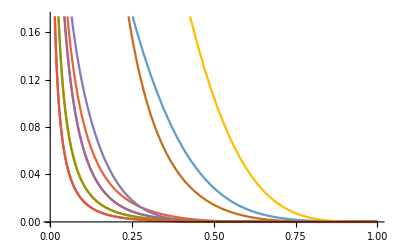

```mathematica
Plot[
Table[ x pdf[iset0,iPart,x,q0],{iPart,-5,5}] //Evaluate
,{x,10^-3,1}]
```

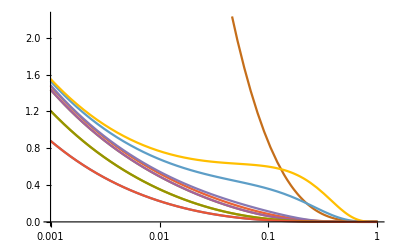

```mathematica
LogLinearPlot[
Table[ x pdf[iset0,iPart,x,q0],{iPart,-5,5}] //Evaluate
,{x,10^-3,1}]
```

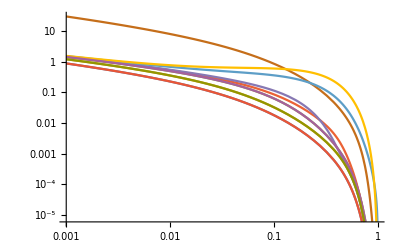

```mathematica
LogLogPlot[
Table[ x pdf[iset0,iPart,x,q0],{iPart,-5,5}] //Evaluate
,{x,10^-3,1}]
```

#### Plot single flavor of multiple PDF

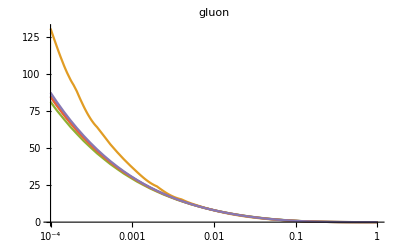

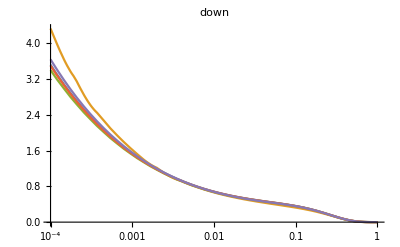

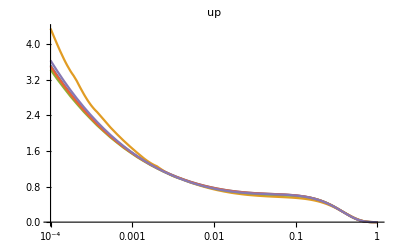

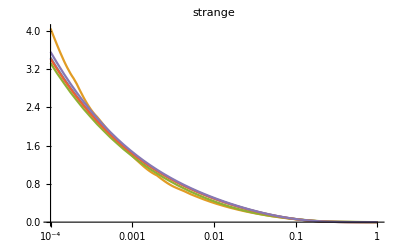

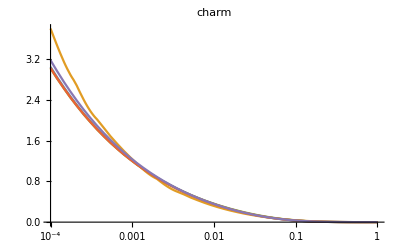

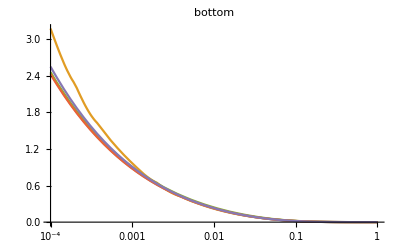

```mathematica
Do[
LogLinearPlot[
Table[ x pdf[setList[[i]],ipart,x,q0],{i,1,Length[setList]}] //Evaluate
,{x,10^-4,1},PlotLabel->pdfFlavor[ipart]]  //Print
,{ipart,0,5}]
```

#### Plot Ratios of single flavor of multiple PDF

ManeParse cubic interpolation will be used.

The x-power of the interpolation is set to 1

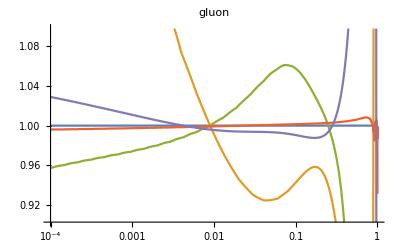

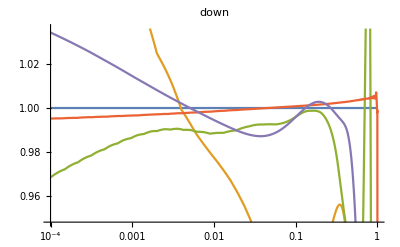

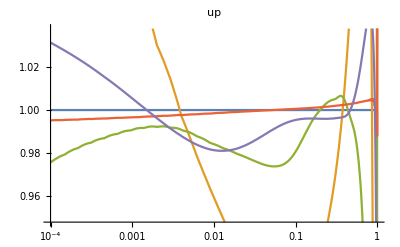

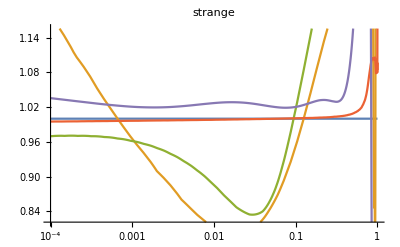

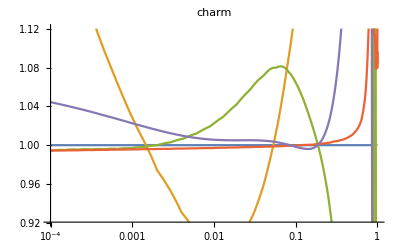

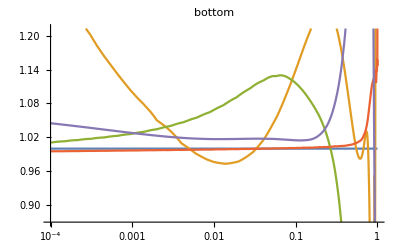

```mathematica
pdfSetXpower[1]

Do[
LogLinearPlot[
Table[  pdf[setList[[i]],ipart,x,q0]/pdf[setList[[1]],ipart,x,q0],{i,1,Length[setList]}] //Evaluate
,{x,10^-4,1},PlotLabel->pdfFlavor[ipart]]  //Print
,{ipart,0,5}]
```

## Speed Test: 1000 calls of each set

```mathematica
pdfSetInterpolator["MMA"]
```

Default Mathematica interpolator will be used.

```mathematica
fullSetList={ct10,mstw,nnpdf,ct10pds,cteq66};
setList=First /@ fullSetList
```

{1,54,95,196,248}

```mathematica
q0=10.;
Do[
Print["iset =",setList[[i]]];
Table[pdf[setList[[i]],RandomInteger[{-5,5}],RandomReal[],q0],{j,1000}] //Timing //First //Print;
,{i,1,Length[setList]}]
```

iset =1

0.734992

iset =54

0.612173

iset =95

0.770472

iset =196

0.732774

iset =248

0.730468

## Error PDF w/ Hessian sets

```mathematica
xlist=Table[10.^i,{i,-4,0,1/8}] //Drop[#,-1]&
```

{0.0001,0.000133352,0.000177828,0.000237137,0.000316228,0.000421697,0.000562341,0.000749894,0.001,0.00133352,0.00177828,0.00237137,0.00316228,0.00421697,0.00562341,0.00749894,0.01,0.0133352,0.0177828,0.0237137,0.0316228,0.0421697,0.0562341,0.0749894,0.1,0.133352,0.177828,0.237137,0.316228,0.421697,0.562341,0.749894}

```mathematica
pdf[cteq66,0,0.1,10.]
```

{11.0883,11.1187,11.0573,11.1202,11.0572,11.0862,11.0903,11.2019,10.9682,11.2574,10.9013,11.3857,10.7655,10.9657,11.2108,11.0705,11.1066,11.1095,11.0642,11.0989,11.0751,10.9216,11.2274,11.1034,11.072,11.1813,10.9852,11.0453,11.1219,11.0529,11.1283,10.9425,11.194,11.0119,11.1392,11.1182,11.0519,10.8565,11.3081,11.1406,11.0347,11.1061,11.0658,11.082,11.0617}

```mathematica
?pdfHessianError
```

```mathematica
pdfHessianError[pdf[cteq66,0,0.1,10.]]
```

0.520415

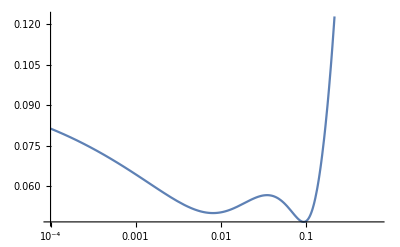

```mathematica
ipart0=0;
q0=10.;
LogLinearPlot[pdfHessianError[pdf[cteq66,ipart0,x,q0]]/pdf[cteq66[[1]],ipart0,x,q0],{x,10.^-4,0.7}]
```

```mathematica
central=pdf[cteq66[[1]],ipart0,#,q0]& /@ xlist
```

{380767.,260692.,178178.,121603.,82842.7,56333.9,38224.,25881.3,17480.9,11775.3,7907.2,5292.29,3528.32,2341.95,1546.03,1014.43,660.461,426.012,271.568,170.516,105.053,63.1767,36.8505,20.691,11.0883,5.618,2.66386,1.16846,0.467216,0.166503,0.0492013,0.00729601}

```mathematica
error=pdfHessianError[pdf[cteq66,ipart0,#,q0]]& /@ xlist
```

{30982.9,20777.3,13880.2,9238.42,6122.95,4040.23,2652.71,1733.19,1126.33,728.137,468.283,299.938,191.603,122.434,78.5327,50.7992,33.2095,21.9059,14.4603,9.41753,5.94106,3.55473,1.97668,1.01649,0.520415,0.321429,0.233165,0.164019,0.10583,0.062599,0.0314524,0.00786853}

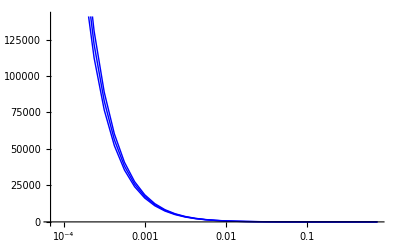

```mathematica
mid=Transpose[{xlist,central}];
up=Transpose[{xlist,central+error}];
down=Transpose[{xlist,central-error}];

ListLogLinearPlot[ {up,mid,down},
Joined->True,
Filling->{2},
FillingStyle->LightBlue,
PlotStyle->({#,Blue}& /@  {Thin,Thick,Thin})
]
```

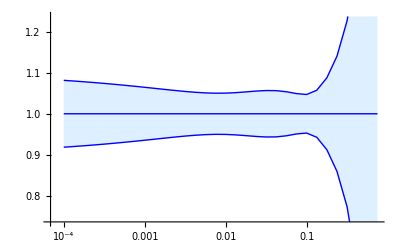

```mathematica
mid=Transpose[{xlist,central/central}];
up=Transpose[{xlist,(central+error)/central}];
down=Transpose[{xlist,(central-error)/central}];

ListLogLinearPlot[ {up,mid,down},
Joined->True,
Filling->{2},
FillingStyle->LightBlue,
PlotStyle->({#,Blue}& /@  {Thin,Thick,Thin})
]
```

## Error PDF w/ MC sets

```mathematica
xlist=Table[10.^i,{i,-4,0,1/8}] //Drop[#,-1]&
```

{0.0001,0.000133352,0.000177828,0.000237137,0.000316228,0.000421697,0.000562341,0.000749894,0.001,0.00133352,0.00177828,0.00237137,0.00316228,0.00421697,0.00562341,0.00749894,0.01,0.0133352,0.0177828,0.0237137,0.0316228,0.0421697,0.0562341,0.0749894,0.1,0.133352,0.177828,0.237137,0.316228,0.421697,0.562341,0.749894}

```mathematica
pdf[nnpdf,0,0.1,10.]
```

{12.207,12.5159,12.3313,12.6324,11.88,12.4589,12.3173,12.1461,12.1531,12.5251,12.2188,11.5647,12.3295,11.6583,12.2525,12.4926,12.4428,12.3161,12.4497,12.2567,12.9039,12.2476,12.1758,12.2701,12.3423,12.0201,12.3131,12.2846,12.1049,12.6721,12.6727,12.0485,11.939,11.8537,12.2906,12.3333,11.9892,12.3866,12.1174,12.2578,11.9409,12.2117,12.143,12.0268,12.4167,12.2573,12.4035,12.1066,12.224,12.1717,12.0302,12.1057,12.1563,12.4831,11.682,11.9222,12.3201,12.0099,12.0033,12.7423,12.1389,12.1197,12.5887,11.7591,12.2829,12.051,12.148,12.7144,12.163,11.7889,11.7722,11.9971,12.324,12.088,12.4275,12.1174,12.0023,11.9895,12.1092,12.1207,11.9701,12.2022,11.8597,12.8039,12.1035,12.2958,12.0569,12.3436,12.1236,12.592,12.0457,12.0285,12.043,12.3269,12.5831,12.1724,12.205,12.212,12.0737,12.1698,12.2588}

```mathematica
?pdfMCError
```

```mathematica
pdfMCError[pdf[nnpdf,0,0.1,10.]]
```

0.248746

```mathematica
ipart0=0;
q0=10.;
(* THIS TAKES A LONG TIME
LogLinearPlot[pdfMCError[pdf[nnpdf,ipart0,x,q0]]/pdf[nnpdf[[1]],ipart0,x,q0],{x,10.^-4,0.7}]
*)
```

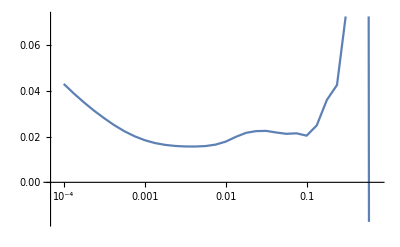

```mathematica
ListLogLinearPlot[
Transpose[{xlist,(pdfMCError[pdf[nnpdf,ipart0,#,q0]]/pdf[nnpdf[[1]],ipart0,#,q0])& /@ xlist}]
,Joined->True]
```

```mathematica
central=pdf[nnpdf[[1]],ipart0,#,q0]& /@ xlist
```

{337356.,232042.,159521.,109549.,75101.3,51310.2,34997.4,23834.7,16203.,10979.,7414.15,4995.76,3356.82,2246.81,1493.12,987.221,648.563,422.67,272.164,172.957,108.225,66.2964,39.4227,22.49,12.207,6.16079,2.88124,1.24194,0.479058,0.151288,0.0246692,-0.00145215}

```mathematica
error=pdfMCError[pdf[nnpdf,ipart0,#,q0]]& /@ xlist
```

{14502.7,9003.64,5567.8,3427.03,2102.27,1279.47,780.347,479.487,298.252,188.497,121.336,79.3764,52.5759,35.137,23.6488,16.2579,11.521,8.39164,5.87751,3.86822,2.43145,1.443,0.835067,0.481493,0.248746,0.153142,0.103677,0.0527781,0.0370578,0.0285079,0.0127916,0.00411808}

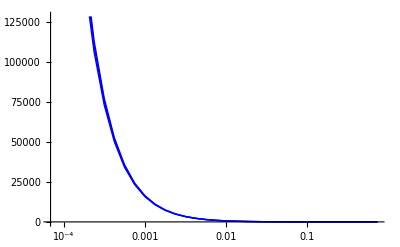

```mathematica
mid=Transpose[{xlist,central}];
up=Transpose[{xlist,central+error}];
down=Transpose[{xlist,central-error}];

ListLogLinearPlot[ {up,mid,down},
Joined->True,
Filling->{2},
FillingStyle->LightBlue,
PlotStyle->({#,Blue}& /@  {Thin,Thick,Thin})
]
```

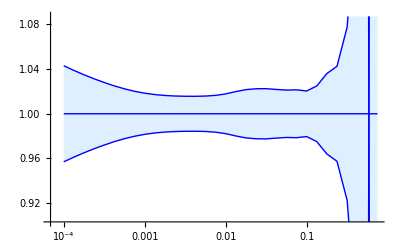

```mathematica
mid=Transpose[{xlist,central/central}];
up=Transpose[{xlist,(central+error)/central}];
down=Transpose[{xlist,(central-error)/central}];

ListLogLinearPlot[ {up,mid,down},
Joined->True,
Filling->{2},
FillingStyle->LightBlue,
PlotStyle->({#,Blue}& /@  {Thin,Thick,Thin})
]
```

## Luminosity

```mathematica
?pdfLuminosity
```

```mathematica
pdfLuminosity[1,14000,80.3,1,-2]
```

0.00125959

```mathematica
massTable=Table[10.^i,{i,1,3,1/10}]
```

{10.,12.5893,15.8489,19.9526,25.1189,31.6228,39.8107,50.1187,63.0957,79.4328,100.,125.893,158.489,199.526,251.189,316.228,398.107,501.187,630.957,794.328,1000.}

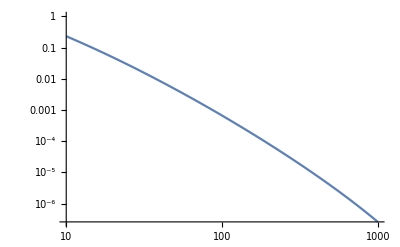

```mathematica
LogLogPlot[pdfLuminosity[1,14000,m,1,-2],{m,10.,1000}]
```

```mathematica
lum[i_]:=lum[i]=Transpose[{massTable, pdfLuminosity[1,14000,#,i,-i]& /@ massTable}]
```

```mathematica
Table[lum[i],{i,1,5}];
```

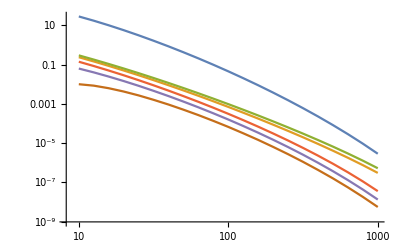

```mathematica
ListLogLogPlot[Table[lum[i],{i,0,5}],Joined->True]
```

## Alpha-s

```mathematica
?pdfAlphaS
```

```mathematica
setList
```

{1,54,95,196,248}

```mathematica
Table[{setList[[i]],pdfAlphaS[setList[[i]],91.2]},{i,1,Length[setList]}] //TableForm
```

Created pdfAlphaS for iSet = 1

1 has  1 sub-grid

Created pdfAlphaS for iSet = 54

PDF Set = 54 has  3 sub-grids

Created pdfAlphaS for iSet = 95

PDF Set = 95 has  3 sub-grids

1 | 0.117998
54 | 0.139384
95 | 0.118003
196 | Null[]
248 | Null[]

```mathematica
pdfSetList[[setList]] //TableForm
```

1 | /usr/local/share/LHAPDF/CT10nlo/CT10nlo_0000.dat | 5 | n/a
54 | /usr/local/share/LHAPDF/MSTW2008lo68cl/MSTW2008lo68cl_0000.dat | 5 | n/a
95 | /usr/local/share/LHAPDF/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118_0000.dat | 5 | n/a
196 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ct10.pds/ct10.00.pds | 5 | 2
248 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/PDFDIR/PDS/ctq66m.pds/ctq66.00.pds | 5 | 2

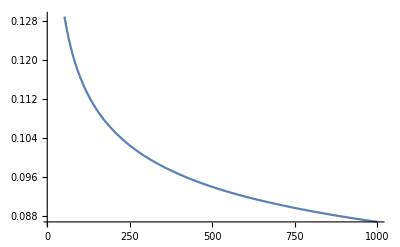

```mathematica
Plot[pdfAlphaS[1,q],{q,10,1000}]
```

## Small x

```mathematica
?pdfLowFunction
```

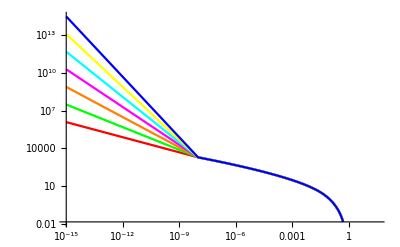

```mathematica
LogLogPlot[
Table[pdfLowFunction[1,0,x,100.,i],{i,0.4,1.6,0.2}]//Evaluate,
{x,10.^-15,0.5},
PlotRange->{{Log[10^-1],Log[10^15]},All},
PlotStyle->{Red,Green,Orange,Magenta,Cyan,Yellow,Blue,Purple}
]
```